# MGDrivE: Software Paper Data Analysis

## Functions And Constants

```mathematica
SetDirectory[NotebookDirectory[]]
baseFolders={baseFolderRIDL,baseFolderWolbachia,baseFolderWolbachiaRadiation,baseFolderCRISPRSIT,baseFolderfsRIDL,basefsRIDLEgg,baseRIDLEgg}={"RIDL/","Wolbachia/","WolbachiaRadiation/","CRISPR_SIT/","fsRIDL/","fsRIDL_Egg/","RIDL_Egg/"}
{repFolderRIDL,repFolderWolbachia,repFolderWolbachiaRadiation,repFolderCRISPRSIT,repFolderfsRIDL,repFolderfsRIDLEgg,repFolderRIDLEgg}=(#<>"Repetitions/")&/@baseFolders
{meanFolderRIDL,meanFolderWolbachia,meanFolderWolbachiaRadiation,meanFolderCRISPRSIT,meanFolderfsRIDL,meanFolderfsRIDLEgg,meanFolderRIDLEgg}=(#<>"Mean/")&/@baseFolders
(*Functions*)
ImportAndReshapeData[folderName_]:=Module[{fileNames,raw,data,dataTotal,maleFileNames,femaleFileNames,rawMale,rawFemale,dataMale,dataFemale,dataTotalMale,dataTotalFemale,genotypes},
fileNames={maleFileNames,femaleFileNames}=FileNames[folderName<>"/"<>#]&/@{"ADM*.csv","AF1*.csv"};
raw={rawMale,rawFemale}=Table[ParallelMap[Import[#]&,i],{i,fileNames}];
data={dataMale,dataFemale}=Table[#[[2;;All,3;;All]]&/@i,{i,raw}];
dataTotal={dataTotalMale,dataTotalFemale}=Table[Flatten/@Transpose[{Total/@#,#}]&/@i,{i,data}];
genotypes=Prepend[rawMale[[1,1,3;;All]],"Total"];
{genotypes,dataTotal}
]
CreateColorBlend[genotypes_,colorSchemeName_,{markerSize_,labelStyle_}]:=Module[{colorPalette,colorPairs,colorSwatch},
colorPalette=Prepend[ColorData[colorSchemeName][#]&/@Range[0,1,1/(Length[genotypes]-1)],Lighter[Black,.75]];
colorPairs=Transpose[{Prepend[genotypes[[All,1]],"Total"],colorPalette}];
colorSwatch=SwatchLegend[colorPairs[[All,2]],colorPairs[[All,1]],LegendMarkerSize->markerSize,LabelStyle->labelStyle,LegendLayout->{"Column",1}];
{colorPalette,colorSwatch}
]
AggregatePopulationByGenotypeIndices[populationDatasets_,genotypesIndicesToAggregate_]:=Module[{popsDatasets,geneLabels},
popsDatasets=Table[Transpose[Total/@populationDatasets[[i,All,#[[2]]]]&/@genotypesIndicesToAggregate],{i,1,Length[populationDatasets]}];
geneLabels=genotypesIndicesToAggregate[[All,1]];
{geneLabels,AddTotalPopulationToDataset[popsDatasets]}
]
AddTotalPopulationToDataset[dataset_]:=Table[Append[#,Total[#]]&/@dataset[[i]],{i,1,Length[dataset]}]
(**)
{topRangeGlobal,topTimeGlobal}={12000,400};
Themes`AddThemeRules["BrushStrokes",
dataAggregateTransposed[[All,i]]/2
,AspectRatio->1/5
,Frame->True
,FrameLabel->Map[Style[#,30]&,{{"Allele Count",Rotate["",-90Degree]},{"Time",""}},{2}]
,FrameStyle->Directive[Thickness[.00125]]
,FrameTicks->{{Range[0,topRangeGlobal,5000],None},{Range[0,topTimeGlobal,200],None}}
,FrameTicksStyle->Directive[20]
,ImageSize->1500
,PerformanceGoal->"Speed"
,PlotRange->{{0,topTimeGlobal},{0,topRangeGlobal}}
,DefaultPlotStyle->Thread@Directive[Thickness[.00075],Opacity[.025]]
,Epilog->Flatten[{
Thickness[.000075],Line[{{#,0},{#,topRange}}]&/@releasesPattern,
Opacity[0],LightRed,EdgeForm[Directive[Thickness[.000075]]],
Rectangle[{Min[releasesPattern],0},{Max[releasesPattern],topRange}]
}]
]
```

/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/CRISPR_SIT

{RIDL/,Wolbachia/,WolbachiaRadiation/,CRISPR_SIT/,fsRIDL/,fsRIDL_Egg/,RIDL_Egg/}

{RIDL/Repetitions/,Wolbachia/Repetitions/,WolbachiaRadiation/Repetitions/,CRISPR_SIT/Repetitions/,fsRIDL/Repetitions/,fsRIDL_Egg/Repetitions/,RIDL_Egg/Repetitions/}

{RIDL/Mean/,Wolbachia/Mean/,WolbachiaRadiation/Mean/,CRISPR_SIT/Mean/,fsRIDL/Mean/,fsRIDL_Egg/Mean/,RIDL_Egg/Mean/}

Part::pkspec1: The expression i cannot be used as a part specification.

BrushStrokes

## Paper Plots

μ Sweep

```mathematica
SetDirectory[NotebookDirectory[]];
folders=FileNames[Directory[]<>"/ParameterSweeps/LifespanReduction/Repetitions/"<>"0*"]//Reverse;
levels=ToExpression[Last/@(StringSplit[#,"/"]&/@folders)]/1000//N;
wildIndex=1;
genotypesIndicesToAggregate={
{"W",{1,1,2}},
{"R",{2,3,3}}
};
(**)
dataTotals=ParallelTable[
folder=folders[[i]];
files={filesMale,filesFemale}={FileNames[folder<>"/ADM*"],FileNames[folder<>"/AF1_Aggregate*"]};
{dataMale,dataFemale}=Table[Import[#][[2;;All,3;;All]]&/@i,{i,files}];
dataTotal=dataFemale(*dataFemale(*(dataMale+dataFemale)*)*);
dataAggregate=AggregatePopulationByGenotypeIndices[dataTotal,genotypesIndicesToAggregate][[2]];
dataAggregateTransposed=Transpose/@dataAggregate;
Median/@(dataAggregateTransposed//Transpose)//N
,{i,1,Length[folders]}];
```

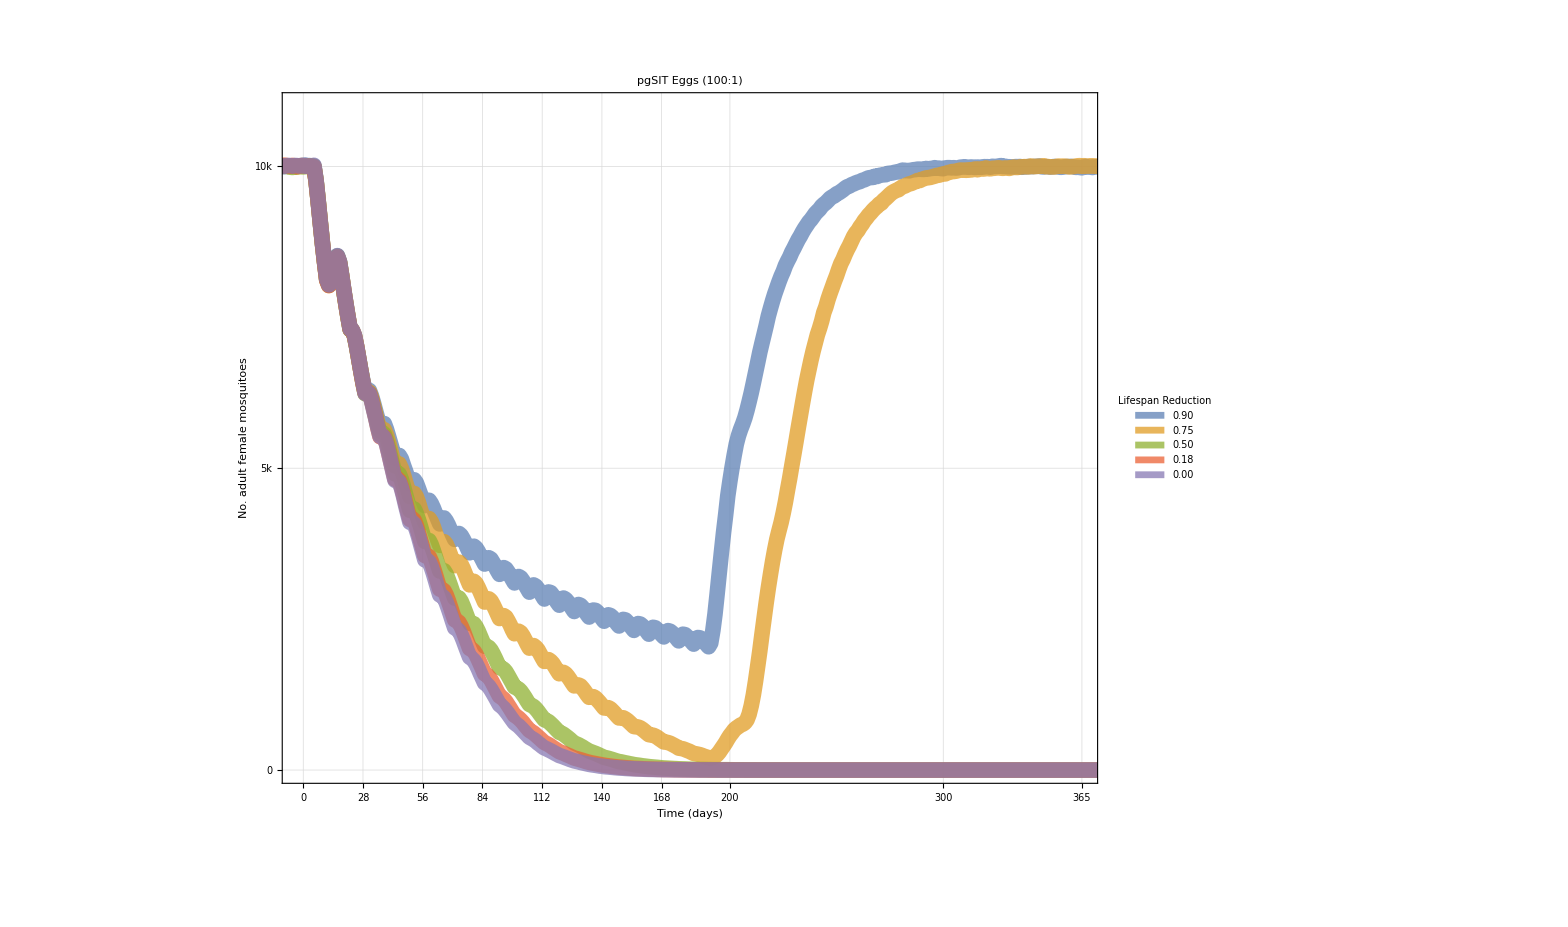

Lifespan100Line.pdf

```mathematica
listLine=ListLinePlot[dataTotals[[1;;All,wildIndex]]/2
,Frame->True
,FrameLabel->(Style[#,75]&/@{"Time (days)","No. adult female\nmosquitoes"})
,FrameStyle->Thick
,FrameTicks->{
{{{0,0},{5000,"5k"},{10000,"10k"}},None},
{{{0*(7*4)+20,0*7*4},{1*(7*4)+20,1*7*4},{2*(7*4)+20,2*7*4},{3*(7*4)+20,3*7*4},{4*(7*4)+20,4*7*4},{5*(7*4)+20,5*7*4},{6*(7*4)+20,6*7*4},{220,200},{320,300},{365+20,365},{420,400}},None}
}
,FrameTicksStyle->40
,GridLines->Automatic
,GridLinesStyle->Directive[Thick,Opacity[.15]]
,ImageSize->1500
,PlotLabel->Style["pgSIT Eggs (100:1)",100]
,PlotRange->{{17.5,365+20},{0,11000}}
,PlotStyle->{Directive[Opacity[.75],Thickness[.0075]]}
,PlotLegends->SwatchLegend[Automatic,StringPadRight[#,4,"0"]&/@(ToString/@levels),LegendMarkerSize->50,LabelStyle->40,LegendLabel->Style["Lifespan\nReduction",40]]
]
Export["Lifespan100Line.pdf",listLine]
```

## 150:1

```mathematica
SetDirectory[NotebookDirectory[]];
folders=FileNames[Directory[]<>"/Output/SW2/Repetitions150/"<>"0*"];
levels=ToExpression[Last/@(StringSplit[#,"/"]&/@folders)]/1000//N;
wildIndex=1;
genotypesIndicesToAggregate={
{"W",{1,1,2}},
{"R",{2,3,3}}
};
(**)
dataTotals=ParallelTable[
folder=folders[[i]];
files={filesMale,filesFemale}={FileNames[folder<>"/ADM*"],FileNames[folder<>"/AF1_Aggregate*"]};
{dataMale,dataFemale}=Table[Import[#][[2;;All,3;;All]]&/@i,{i,files}];
dataTotal=dataFemale(*dataFemale(*(dataMale+dataFemale)*)*);
dataAggregate=AggregatePopulationByGenotypeIndices[dataTotal,genotypesIndicesToAggregate][[2]];
dataAggregateTransposed=Transpose/@dataAggregate;
Median/@(dataAggregateTransposed//Transpose)//N
,{i,1,Length[folders]}];
```

```mathematica
matrix=MatrixPlot[dataTotals[[All,wildIndex]]/2
,AspectRatio->1/1.5
,ColorFunction->ColorData[{"LakeColors",{1,.5}}]
,Frame->True
,FrameLabel->(Style[#,50]&/@{"Lifespan Reduction","Time"})
,FrameStyle->Thick
,FrameTicks->{{{Range[Length[levels]],StringPadRight[#,5,"0"]&/@(ToString/@levels)}//Transpose,{Range[Length[levels]],StringPadRight[#,5,"0"]&/@(ToString/@levels)}//Transpose},{Automatic,Automatic}}
,FrameTicksStyle->20
,ImageSize->2000
,Mesh->{True,None}
,MeshStyle->Thin
,PlotLabel->Style["Releasing pgSIT Eggs at a 150:1 Ratio",75]
,PlotLegends->BarLegend[Automatic,LegendLabel->Placed[Style["No. adult female mosquitoes",30],Top],LabelStyle->25,LegendMargins->{{0,0},{25,25}}]
,PlotRangePadding->None
];
Export["Lifespan150.pdf",matrix]
```

Lifespan150.pdf

ξ Sweep

```mathematica
SetDirectory[NotebookDirectory[]];
folders=FileNames[Directory[]<>"/ParameterSweeps/MatingEfficacy/Repetitions/"<>"0*"];
levels=ToExpression[Last/@(StringSplit[#,"/"]&/@folders)]/1000//N;
wildIndex=1;
genotypesIndicesToAggregate={
{"W",{1,1,2}},
{"R",{2,3,3}}
};
(**)
dataTotals=ParallelTable[
folder=folders[[i]];
files={filesMale,filesFemale}={FileNames[folder<>"/ADM*"],FileNames[folder<>"/AF1_Aggregate*"]};
{dataMale,dataFemale}=Table[Import[#][[2;;All,3;;All]]&/@i,{i,files}];
dataTotal=dataFemale(*dataFemale(*(dataMale+dataFemale)*)*);
dataAggregate=AggregatePopulationByGenotypeIndices[dataTotal,genotypesIndicesToAggregate][[2]];
dataAggregateTransposed=Transpose/@dataAggregate;
Median/@(dataAggregateTransposed//Transpose)//N
,{i,1,Length[folders]}];
```

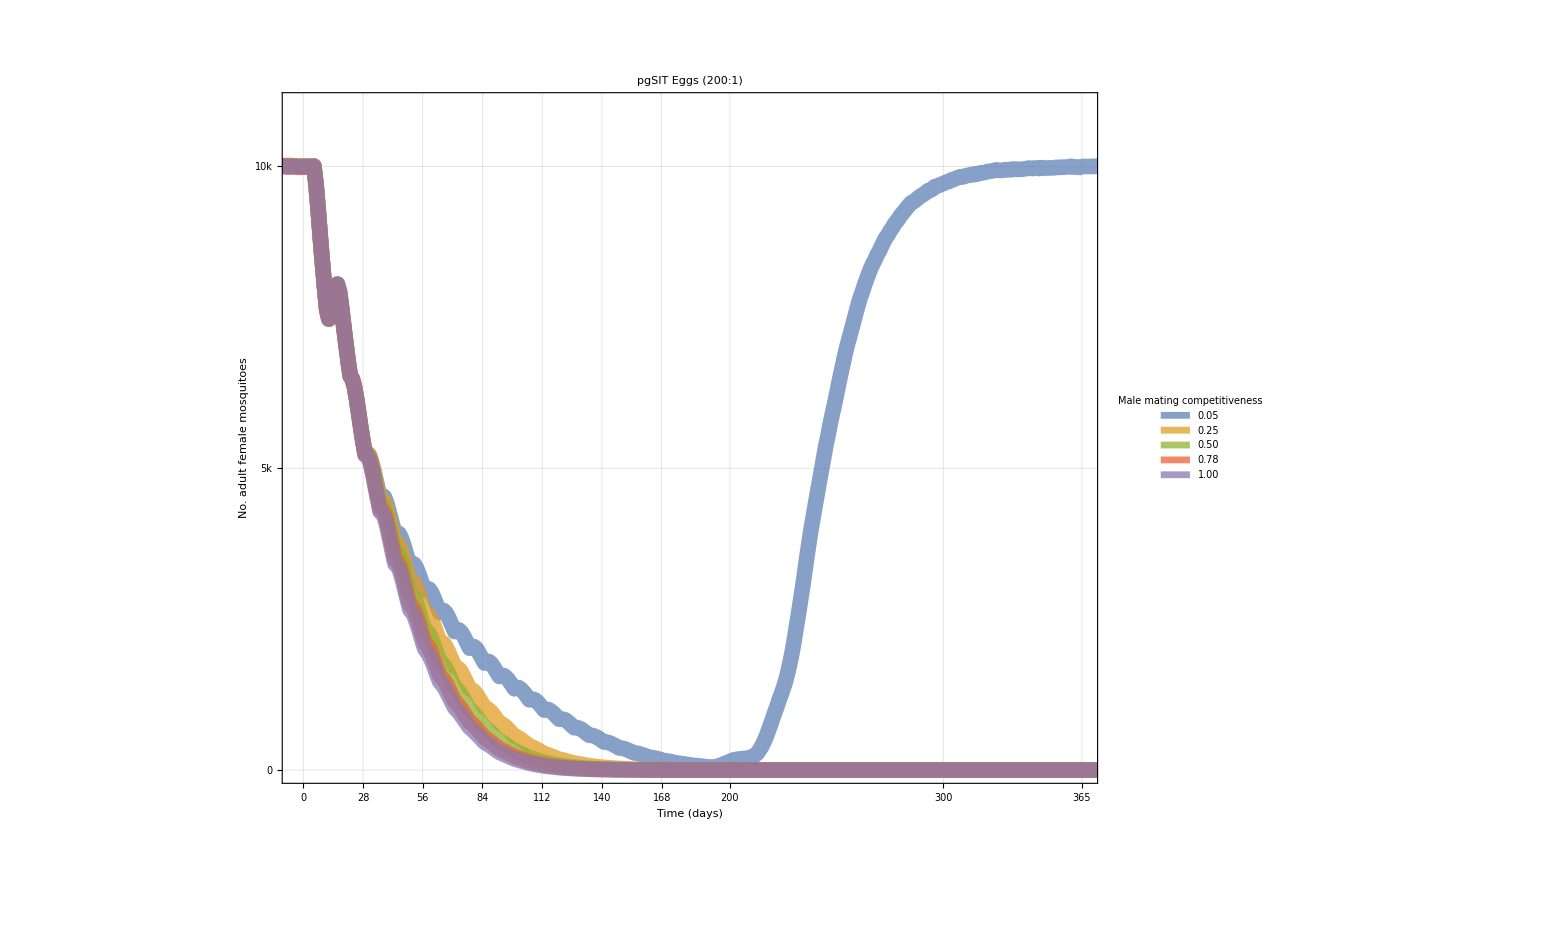

Mating100Line.pdf

```mathematica
listLine=ListLinePlot[dataTotals[[All,wildIndex]]/2
,Frame->True
,FrameLabel->(Style[#,75]&/@{"Time (days)","No. adult female\nmosquitoes"})
,FrameStyle->Thick
,FrameTicks->{
{{{0,0},{5000,"5k"},{10000,"10k"}},None},
{{{0*(7*4)+20,0*7*4},{1*(7*4)+20,1*7*4},{2*(7*4)+20,2*7*4},{3*(7*4)+20,3*7*4},{4*(7*4)+20,4*7*4},{5*(7*4)+20,5*7*4},{6*(7*4)+20,6*7*4},{220,200},{320,300},{365+20,365},{420,400}},None}
}
,FrameTicksStyle->40
,GridLines->Automatic
,GridLinesStyle->Directive[Thick,Opacity[.15]]
,ImageSize->1500
,PlotLabel->Style["pgSIT Eggs (200:1)",100]
,PlotRange->{{17.5,365+20},{0,11000}}
,PlotStyle->{Directive[Opacity[.75],Thickness[.0075]]}
,PlotLegends->SwatchLegend[Automatic,StringPadRight[#,4,"0"]&/@(ToString/@levels),LegendMarkerSize->50,LabelStyle->35,LegendLabel->Style["Male mating\ncompetitiveness",40]]
]
Export["Mating100Line.pdf",listLine]
```

μ and ξ Sweep

```mathematica
SetDirectory[NotebookDirectory[]];
folders=FileNames[Directory[]<>"/ParameterSweeps/LifespanAndMatinFactorial/"<>"*0"];
levels=ToExpression[(StringSplit[#,"_"]&/@(Last/@(StringSplit[#,"/"]&/@folders)))]/1000//N;
```

```mathematica
wildIndex=1;
genotypesIndicesToAggregate={
{"W",{1,1,2}},
{"R",{2,3,3}}
};
(**)
dataTotals=ParallelTable[
folder=folders[[i]];
files={filesMale,filesFemale}={FileNames[folder<>"/ADM*"],FileNames[folder<>"/AF1_Aggregate*"]};
{dataMale,dataFemale}=Table[Import[#][[2;;All,3;;All]]&/@i,{i,files}];
dataTotal=dataFemale(*dataFemale(*(dataMale+dataFemale)*)*);
dataAggregate=AggregatePopulationByGenotypeIndices[dataTotal,genotypesIndicesToAggregate][[2]];
dataAggregateTransposed=Transpose/@dataAggregate;
Median/@(dataAggregateTransposed//Transpose)//N
,{i,1,Length[folders]}];
```

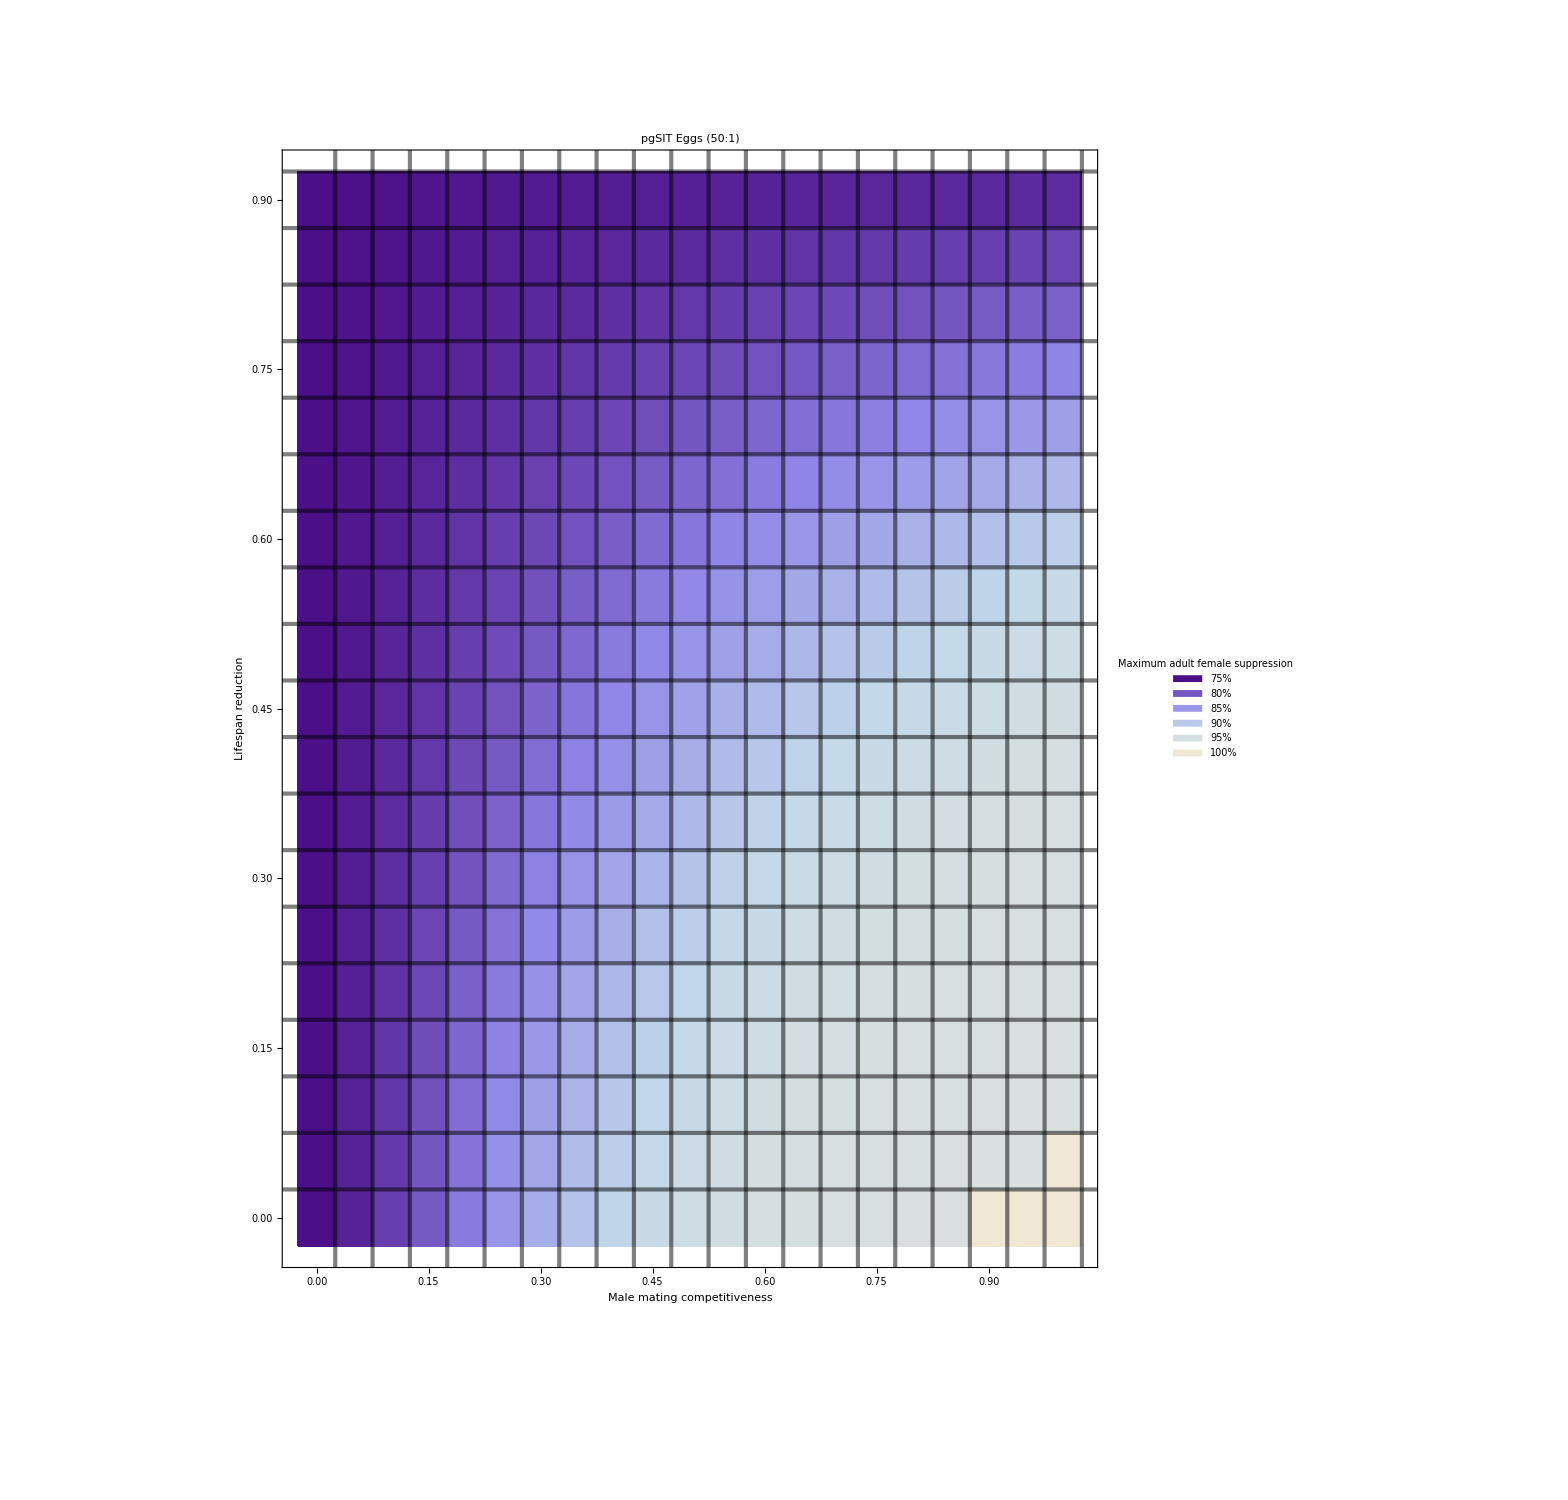

FactorialSweep.pdf

```mathematica
minPopValues=Min/@(dataTotals[[All,wildIndex]]/2);
tuples=Flatten/@Transpose[{levels,ReplaceAll[Chop[minPopValues],{0->-1000}]}];
fixedTuples=Map[Chop,tuples,Infinity];
(**)
colorLevels=ColorData[{"LakeColors","Reverse"}][#1]&/@Reverse[Range[0,1,.2]];
popValues=Reverse[Range[0,Max[minPopValues]-1,(Max[minPopValues]-Min[minPopValues])/Length[colorLevels]]];
swatch=SwatchLegend[colorLevels,{"75%","80%","85%","90%","95%","100%"},LegendMarkerSize->50,LabelStyle->50,LegendLabel->Style["Maximum adult\nfemale suppression",50],LegendLayout->"Column"];
(**)
density=ListDensityPlot[{#[[1]],#[[2]],#[[3]]}&/@fixedTuples
,AspectRatio->1
,ColorFunction->ColorData[{"LakeColors","Reverse"}]
,ColorFunctionScaling->True
,FrameLabel->{Style["Male mating competitiveness",75],Style["Lifespan reduction",75]}
,FrameTicksStyle->40
,FrameStyle->Thick
,ImageSize->1500
,InterpolationOrder->0
,MaxPlotPoints->Infinity
,Mesh->{20,18}
,MeshStyle->None
,PlotLabel->Style["pgSIT Eggs (50:1)",80]
,PlotLegends->Placed[swatch,Right]
,PlotRange->{{-.025,1.025},{-.025,.925}}
,PlotRangePadding->0
,Epilog->Flatten[{
Opacity[0],
Disk[#,0.0025]&/@fixedTuples[[All,1;;2]],
Opacity[0.5],Thickness[.002],
Line[{{#+.025,-5},{#+.025,5}}]&/@tuples[[All,1]]//DeleteDuplicates,
Line[{{-1,#+.025},{2,#+.025}}]&/@tuples[[All,2]]//DeleteDuplicates
}]
]
Export["FactorialSweep.pdf",density]
```